8.18182

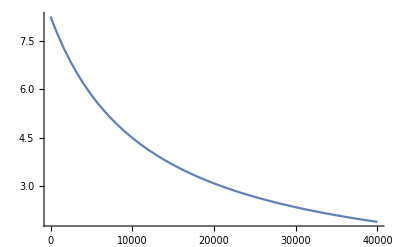

{{Rs→ConditionalExpression[√(dR Rl+Rl^2),Rl>0&&dR>0]}}

{{Rs→√(Rl (dR+Rl))}}

Rs→6403.12

{7.7843,1.2157,6.56859}

6.56859

```mathematica
rl = 1*^3;
dr = 40*^3;
vcc = 9;

vmax = vcc * Rs/(Rl+Rs);
vmin = vcc * Rs/(Rl+dR+Rs);
N[vmax/.{Rs-> 10*^3, Rl->1*^3}]
v[rl_,dr_,rs_]:= (vcc*rs)/(rl+dr+rs)
Plot[v[rl,ΔR,11*^3],{ΔR, 0, dr}]
dv = vmax-vmin;

sol = Solve[D[dv, Rs] == 0 && Rs>0 && Rl>0 && dR>0 ,Rs]
sol =  Simplify[Refine[sol, Assumptions-> {Rs>0, Rl>0, dR>0}]]
sol /. {dR -> dr, Rl -> rl};
rsmx = N[%[[1]][[1]]]
{vmax, vmin, dv}/.{dR->dr, Rl->rl}/.%
N[dv/.{dR->dr, Rl->rl, rsmx}]
```

```mathematica
{{Rs->-√Rl √(dR+Rl)},{Rs->√Rl √(dR+Rl)}}
```

{{Rs→-√Rl √(dR+Rl)},{Rs→√Rl √(dR+Rl)}}

```mathematica
%/.{dR-> 40*^3, Rl-> 1K}
```

{{Rs→-√K √(40000+K)},{Rs→√K √(40000+K)}}

```mathematica
N[{{Rs->-100 √401},{Rs->100 √401}}]
```

{{Rs→-2002.5},{Rs→2002.5}}

```mathematica
vmax /. {dR->40*^3, Rl->100, Rs->2002.5}
```

8.57194

```mathematica
vmin /. {dR->40*^3, Rl->100, Rs->2002.5}
```

0.428062

```mathematica
ω = 2π (190/60)
r = 0.065/2
v= 0.9 ω r
```

(19 π)/3

0.0325

0.58198

```mathematica
Reduce[vcc*Rs/(Rl+Rs+dR)==4.5 && vcc==9,dR]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

dR==-1. Rl+Rs&&Rs≠0

```mathematica
2002.5-100
```

1902.5

```mathematica
D[vcc*Rs/(Rl+Rs+dR), dR]/.{vcc->9, dR->1902.5, Rs->2002.5, Rl-> 100}
```

-0.0011236

```mathematica
dvdr = D[vcc*Rs/(Rl+Rs+dR)]/.{vcc->9, Rs->2002.5, Rl->100}
drdx = 80/dvdr (*based on scale*)
```

18022.5/(2102.5+dR)

0.0044389 (2102.5+dR)

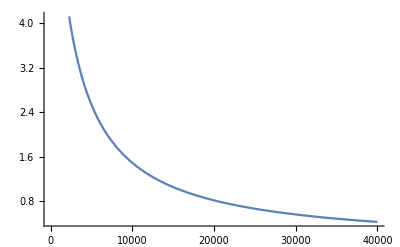

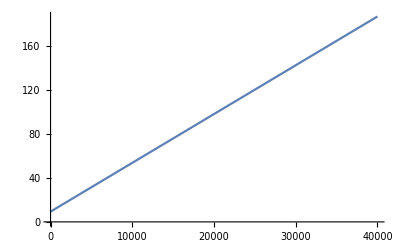

```mathematica
Plot[dvdr, {dR,0,40*^3}]
Plot[drdx, {dR, 0, 40*^3}]
```

```mathematica
drdx/.{dR->0}
```

9.33278

```mathematica
(*kp = rf/ri + ci/cf;
ki = 1/(ri*cf);
kd = rf*ci;*)
(*Eliminate[{kp == rf/ri+ci/cf,ki == 1/(ri*cf),kd == rf*ci,ri==ri}, 
{kp,ki,kd,ri}]
*)
basesol = NSolve[{rf/ri+ci/cf == 0.1,1/(ri cf) == 0.0353, rf*ci ==0.0707}, {cf,ci,rf}]
basesol /. {ri -> 600*^3}
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{cf→28.3286/ri,ci→1.47511/ri,rf→0.0479288 ri},{cf→28.3286/ri,ci→1.35776/ri,rf→0.0520712 ri}}

{{cf→0.0000472144,ci→2.45851×10^-6,rf→28757.3},{cf→0.0000472144,ci→2.26293×10^-6,rf→31242.7}}

```mathematica
Clear[kp]; Clear[ki]; Clear[kd];
```

```mathematica
cost = (rf/ri+ci/cf - 0.1)^2 + (1/(ri cf) - 0.0353)^2 + 0.5*(rf ci - 0.0707)^2
```

0.5 (-0.0707+ci rf)^2+(-0.0353+1/(cf ri))^2+(-0.1+ci/cf+rf/ri)^2

```mathematica
sol = FindMinimum[{cost,ri>20000 , ci>0&&ci<1*^-4, rf>20000, cf>0&&cf<1*^-4}, {ri,ci,rf,cf}]
```

FindMinimum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {2.34961×10^-7,0.000672674,3.97806×10^-8}, is returned.

{5.16447×10^-7,{ri→420817.,ci→2.84228×10^-6,rf→24654.1,cf→0.0000678011}}

```mathematica
{rf/ri+ci/cf, 1/(ri*cf),rf*ci}/.{cf->47*^-6,ci->2.2*^-6,rf->31242,ri->600*^3}
```

{0.0988785,5/141,0.0687324}

```mathematica
62.3*^-6
```

0.0000623

```mathematica
ClearAll["Global`*"]
```